ΜΣΜ 61  
6η Γραπτή Εργασία
Λυμπερίδης Σταύρος   Α.Μ.: 91076

Ασκηση 1

O μετασχηματισμός:

(2 a)/(a^2+ω^2)

Αποτέλεσμα αντιστροφής:

ⅇ^(a x) HeavisideTheta[-x]+ⅇ^(-a x) HeavisideTheta[x]

H συνάρτηση HeavisideTheta συμπεριφέρεται ως εξής:

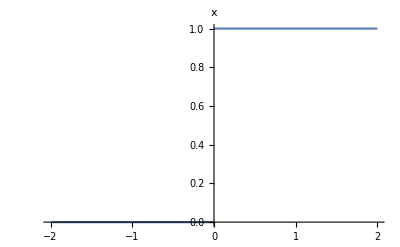

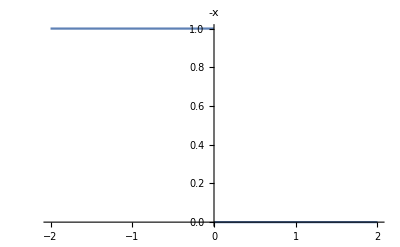

Οπότε παρατηρούμε ότι παίρνουμε την συνάρτηση f(x)

```mathematica
Clear["Global`*"]

f[x_]:=E^(-a*Abs[x])
Print["O μετασχηματισμός:"]
g[ω_]=FourierTransform[f[x],x,ω,FourierParameters->{1,1}]

Print["Αποτέλεσμα αντιστροφής:"]
FullSimplify[InverseFourierTransform[g[ω],ω,x ,FourierParameters->{1,1}],a>0]

Print["H συνάρτηση HeavisideTheta συμπεριφέρεται ως εξής:"]
Plot[HeavisideTheta[x],{x,-2,2},PlotLabel->HeavisideTheta[x]]
Plot[HeavisideTheta[-x],{x,-2,2},PlotLabel->HeavisideTheta[-x]]
Print["Οπότε παρατηρούμε ότι παίρνουμε την συνάρτηση f(x)"]
```

```mathematica
Clear["Global`*"]

f[x_]:=E^(-λ*x^2)
Print["O μετασχηματισμός:"]
g[ω_]=FullSimplify[FourierTransform[f[x],x,ω,FourierParameters->{1,1}],λ>0]
Print["Αποτέλεσμα αντιστροφής:"]
FullSimplify[InverseFourierTransform[g[ω],ω,x ,FourierParameters->{1,1}],λ>0]
```

O μετασχηματισμός:

(ⅇ^(-ω^2/(4 λ)) √π)/(√λ)

Αποτέλεσμα αντιστροφής:

ⅇ^(-x^2 λ)

Ασκηση 2

```mathematica
Clear["Global`*"]

Print["Εφαρμόζοντας τον μετασχηματισμό, καταλήγουμε σε Σ.Δ.Ε. της οποίας η λύση είναι: \nû(ω,t)= c(ω)ⅇ^(-SuperscriptBox[ω, 2] t) "]
f[x_]:=DiracDelta[x]
Print["Εφαρμόζοντας τον μετασχηματισμό για την αρχική συνθήκη στην συνάρτηση δ(x) βρίσκουμε:"]
c[ω_]=FullSimplify[FourierTransform[f[x],x,ω,FourierParameters->{1,1}],λ>0];
Print["û(ω,0)=",c[ω]]
Print["Άρα c(ω)=",c[ω]]
g[ω_]:=E^(-ω^2 *t)
solution[x_,t_]=FullSimplify[InverseFourierTransform[g[ω],ω,x ,FourierParameters->{1,1}],t>0];
Print["Αντιστρέφοντας τον μετασχηματισμό βρίσκουμε την λύση u(x,t)= ",solution[x,t]]

Plot3D[solution[x,t], {t,0,0.001},{x,-10000,10000}]
Manipulate[Plot[solution[x,t],{x,-5,5},PlotRange->{0,9},PlotStyle->{Blue,Thick}],{t,0.001,2,0.0000001}]
```

Εφαρμόζοντας τον μετασχηματισμό, καταλήγουμε σε Σ.Δ.Ε. της οποίας η λύση είναι: 
û(ω,t)= c(ω)ⅇ^(-SuperscriptBox[ω, 2] t)

Εφαρμόζοντας τον μετασχηματισμό για την αρχική συνθήκη στην συνάρτηση δ(x) βρίσκουμε:

û(ω,0)=1

Άρα c(ω)=1

Αντιστρέφοντας τον μετασχηματισμό βρίσκουμε την λύση u(x,t)= (ⅇ^(-x^2/(4 t)))/(2 √π √t)

-Graphics3D-

Ασκηση 3

```mathematica
Clear["Global`*"]

Print["Εφαρμόζοντας τον μετασχηματισμό, καταλήγουμε στη Σ.Δ.Ε.:\nStandardForm`FractionBox[∂, ∂t]StandardForm`OverscriptBox[u, ^] (ω, \ t) = -ω(ω,t) της οποίας η λύση είναι: \nû(ω,t)= A(ω)ⅇ^(-SuperscriptBox[ω, 2] t) \n"]
f[x_]:=DiracDelta[x-a]
Print["Εφαρμόζοντας τον μετασχηματισμό για την συνάρτηση δ(x-a) βρίσκουμε:"]
d[ω_]=FullSimplify[FourierSinTransform[f[x],x,ω],a>0];
Print["δ̂(ω)=",d[ω]]
Print["\nΕφαρμόζοντας την αρχική συνθήκη û(ω,0)=Α(ω)=δ̂(ω)"]


g[ω_]=E^(-ω^2 *t)*d[ω];
Print["Οπότε  û(ω,t)= ",g[ω]]

solution[x_,t_,a_]=FullSimplify[InverseFourierSinTransform[g[ω],ω,x ],{t>0,a>0}];
Print["Αντιστρέφοντας τον μετασχηματισμό βρίσκουμε την λύση u(x,t)= ",solution[x,t,a]]
```

Εφαρμόζοντας τον μετασχηματισμό, καταλήγουμε στη Σ.Δ.Ε.:
StandardForm`FractionBox[∂, ∂t]StandardForm`OverscriptBox[u, ^] (ω, \ t) = -ω(ω,t) της οποίας η λύση είναι: 
û(ω,t)= A(ω)ⅇ^(-SuperscriptBox[ω, 2] t)

Εφαρμόζοντας τον μετασχηματισμό για την συνάρτηση δ(x-a) βρίσκουμε:

δ̂(ω)=√(2/π) Sin[a ω]

Εφαρμόζοντας την αρχική συνθήκη û(ω,0)=Α(ω)=δ̂(ω)

Οπότε  û(ω,t)= ⅇ^(-t ω^2) √(2/π) Sin[a ω]

Αντιστρέφοντας τον μετασχηματισμό βρίσκουμε την λύση u(x,t)= (ⅇ^(-(a-x)^2/(4 t))-ⅇ^(-(a+x)^2/(4 t)))/(2 √π √t)

```mathematica
Plot3D[solution[x,t,1], {t,0,100},{x,0,50},PlotRange->{{0,100},{0,50},{0,0.1}}, PlotLegends->{"a=1"},AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Plot3D[solution[x,t,3], {t,0,100},{x,0,50},PlotRange->{{0,100},{0,50},{0,0.1}},PlotLegends->{"a=3"},AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Plot3D[solution[x,t,10], {t,0,100},{x,0,50},PlotRange->{{0,100},{0,50},{0,0.1}},PlotLegends->{"a=10"},AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[solution[x,t,a],{x,0,20},PlotRange->{0,1},PlotStyle->{Blue,Thick}],{t,0.1,150,0.01},{a,0.1,20}]
```

Παρατηρούμε ότι η τιμή του α εκτός από την αρχική συνθήκη επηρεάζει την διάδοση της θερμότητας με το πέρασμα του χρόνου. Όσο μεγαλύτερη τιμή έχει το α τόσο πιο αργή είναι η διάδοση της θερμότητας.

Ασκηση 4

```mathematica
Clear["Global`*"]

f[x_]=(Sin[x])/x;
Print["Επιβεβαιώνουμε τον μετασχηματισμό:"]
g[x_]=FourierTransform[f[x],x,ω,FourierParameters->{1,1}]
```

Επιβεβαιώνουμε τον μετασχηματισμό:

1/2 π Sign[1-ω]+1/2 π Sign[1+ω]

εφαρμόζοντας την ταυτότητα Plancherel με  f(x) = (Sin(x))/x  έχουμε:

∫_(−∞)^(+∞) |f(x)|^2 dx=∫_(-∞)^(+∞) |f̂(ω)|^2 dω=∫_-1^(+1) π ·π  ⅆω = π^2 ∫_-1^(+1) ⅆω= 2 π^2 

‘Αρα

∫_(-∞)^(+∞) ((Sin(x))/x)^2 ⅆx =  2 π^2

```mathematica
Print["Επαληθεύουμε την ταυτότητα και υπολογίζουμε το ολοκλήρωμα:"]
2*Pi*∫_(-∞)^∞ (f[x])^2ⅆx
∫_(-∞)^∞ (g[ω])^2ⅆω
```

Επαληθεύουμε την ταυτότητα και υπολογίζουμε το ολοκλήρωμα:

2 π^2

2 π^2

Ασκηση 5

α)

Η γενική λύση είναι  u(x,t) = 1/(2 √(πv t))∫_(-∞)^(+∞) e^(-(x-y)^2/(4vt))·f(y)dy

Για να εκφράσουμε την λύση με την βοήθεια της συνάρτησης erf(x)

▸ Χωρίζουμε το διάστημα ολοκλήρωσης σε (-∞,-L) U (-L,L) U (L,+∞)

▸ Χρησιμοποιούμε την αλλαγή μεταβλητής z=(x-y)/(2 √(v t)) .

Εκτελόντας τα παραπάνω βρίσκουμε ότι:

u(x,t) = Τ/2 (  erf((x+L)/(2 √(v t))) - erf((x-L)/(2 √(v t)))  )

```mathematica
Clear["Global`*"]

u[x_,t_,v_,L_,T_]=(Erf[(x+L)/(2*Sqrt[v*t])]-Erf[(x-L)/(2*Sqrt[v*t])])*T/2;

Plot3D[u[x,t,1,2,2],{x,-10,10},{t,0,6},PlotRange-> All,PlotLegends->{"v=1 ,L=2 ,T=2"}]
```

-Graphics3D-

```mathematica
Plot3D[u[x,t,4,2,2],{x,-10,10},{t,0,6},PlotRange-> All,PlotLegends->{"v=4 ,L=2 ,T=2"}]
```

-Graphics3D-

```mathematica
Plot3D[u[x,t,7,2,2],{x,-10,10},{t,0,6},PlotRange-> All,PlotLegends->{"v=7 ,L=2 ,T=2"}]
```

-Graphics3D-

```mathematica
Plot3D[u[x,t,4,3,1],{x,-10,10},{t,0,6},PlotRange-> All,PlotLegends->{"v=4 ,L=3 ,T=1"}]
```

-Graphics3D-

```mathematica
Plot3D[u[x,t,6,3,1],{x,-10,10},{t,0,6},PlotRange-> All,PlotLegends->{"v=6 ,L=3 ,T=1"}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[x,t,v,L,T],{x,-10,10},PlotRange->{0,2}],{t,0.001,20},{v,1,15},{L,1,4},{T,1,4},AnimationRunning->False]
```

Παρατηρούμε ότι την στιγμή t=0 η θερμοκρασία έχει την τιμή T , στο διάστημα [-L,L] ενώ είναι 0 στο υπόλοιπο διάστημα. Με το πέρασμα του χρόνου η θερμοκρασία διαχέεται στα υπόλοιπα σημεία του διαστήματος , αναλόγος με τον συντελεστή ν. Όσο μεγαλύτερος είναι ο συντελεστής τόσο γρηγορότερα διαχέεται η θερμοκρασία.

β)

Ισχύει ότι u(x, t) ≤ Ιο/(2 √(πv t)),   για  t > 0  
με Ιο την ολική αρχική θερμοκρασιακή ποσότητα του σώματος Ιο =∫_(-∞)^(+∞) f(x) dx  
Για την συνάρτηση f(x)=Piecewise[{{T, |x|≤ L}, {0, |x| > L}}] έχουμε:
Ιο =∫_(-∞)^(+∞) f(x) dx=∫_-L^(+L) Tdx=2 L T  επομένως ισχύει ότι:
u(x, t) ≤ (L T)/(√(πv t))

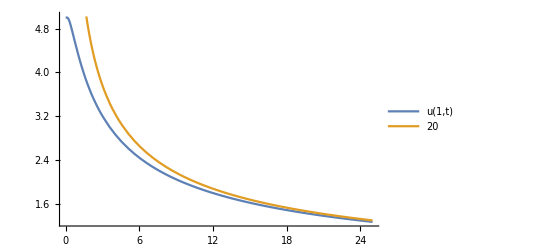

```mathematica
x=1;
t=2;
v=3;
L=4;
T=5;
g[t_]:= (L *T)/( Sqrt[Pi *t* v])
Plot[{u[x,t,v,L,T],g[t]},{t,0,25},PlotLegends->{"u(1,t)","20"}]
```